```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
markers={"■","●","◆","▲","□","○","◇","△"}
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{■,●,◆,▲,□,○,◇,△}

## fig5a

```mathematica
norm[r_]:=Sqrt[r.r];
rh=0.1;
rS=0.11;
Bgeo={0,0,5*10^(-5)}+{{Λ3,0,Λ2},{0,0,0},{Λ2,0,Λ1}}.{x,y,z};
δϕ=Abs@ArcCos@({0,0,1}.Bgeo/norm@Bgeo)//Simplify;
δϕs=δϕ/.{z->Sqrt[rS^2-x^2-y^2]}/.Thread[{Λ1,Λ2,Λ3}->#]&/@{{10^(-5),0,0},{0,10^(-5),0},{0,0,10^(-5)}};
```

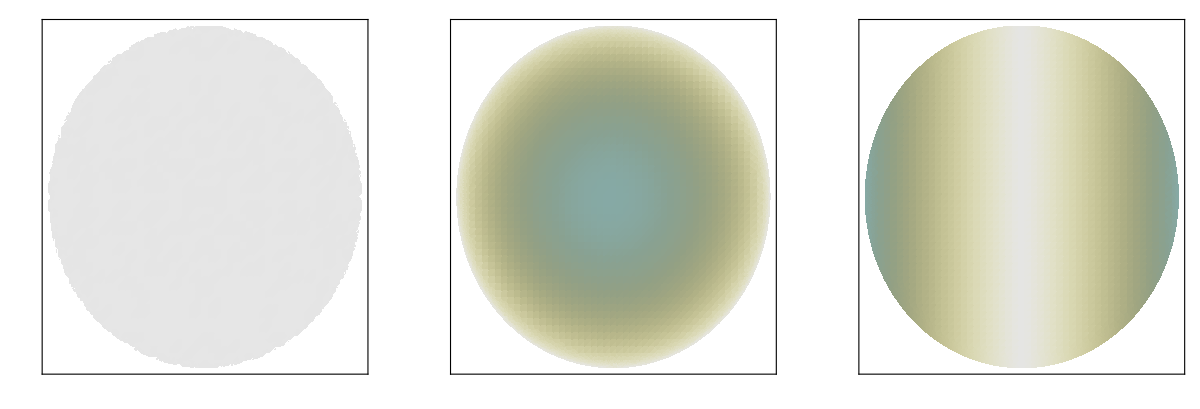

```mathematica
minVal=0;
maxVal=0.025;
ps=DensityPlot[#,{x,y}∈Disk[{0,0},rS],ColorFunctionScaling->False,ColorFunction->Function[f,ColorData["LightTerrain"][1-(f-minVal)/(maxVal-minVal)]],PlotRange->All,FrameLabel->None,FrameTicks->None,PlotPoints->50]&/@δϕs;
bar=BarLegend[{Function[f,ColorData["LightTerrain"][1-(f-minVal)/(maxVal-minVal)]],{minVal,maxVal}}];
p5a=GraphicsRow[Insert[ps,bar,-1],AspectRatio->1/3.5,ImageSize->Full]
```

```mathematica
Export["subplots/fig4a.png",p4a]
```

subplots/fig4a.png

## fig5b-left

data from fig5b-data.py

```mathematica
figID="5b";
names={"3v"}~Join~Table["3s-B"<>s1<>"-1",{s1,{"xx","zx","zz"}}];
d=Length@names;
resultsFilePath="data\\fig"<>figID<>"-"<>#<>".csv"&/@names;
datas=Import/@resultsFilePath;
xs=datas[[;;,1,;;]]*10^7;
ys=datas[[;;,2,;;]];
upper=ys+datas[[;;,3,;;]]/2;
lower=ys-datas[[;;,3,;;]]/2;
Max[upper]
Min[lower]
ys=Table[Transpose@{xs[[i,;;]],ys[[i,;;]]},{i,d}];
upper=Table[Transpose@{xs[[i,;;]],upper[[i,;;]]},{i,d}];
lower=Table[Transpose@{xs[[i,;;]],lower[[i,;;]]},{i,d}];
```

0.0167765

0.00844028

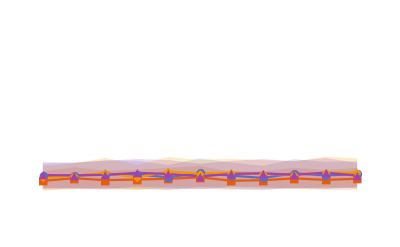

```mathematica
p1=ListPlot[Evaluate@(upper~Join~lower),Joined->True,PlotStyle->None,Filling->Table[{i->{{i+d},Directive[colors[[i]],Opacity[0.2]]}},{i,d}]];
p2=ListLinePlot[Evaluate@ys,PlotMarkers->markers,PlotStyle->colors,PlotTheme->"Scientific",GridLines->None];
p5bl=Show[p1,p2,Axes->False,PlotRange->{{-10,510},{0,0.05}}]
```

```mathematica
Export["subplots/fig5b-left.png",p5bl]
```

subplots/fig5b-left.png

## fig5b-right

data  from  fig5b - data. py

```mathematica
figID="5b";
names={"3v"}~Join~Table["3s-B"<>s1<>"-2",{s1,{"xx","zx","zz"}}];
d=Length@names;
resultsFilePath="data\\fig"<>figID<>"-"<>#<>".csv"&/@names;
datas=Import/@resultsFilePath;
xs=datas[[;;,1,;;]]*10^7;
ys=datas[[;;,2,;;]];
upper=ys+datas[[;;,3,;;]]/2;
lower=ys-datas[[;;,3,;;]]/2;
Max[upper]
Min[lower]
ys=Table[Transpose@{xs[[i,;;]],ys[[i,;;]]},{i,d}];
upper=Table[Transpose@{xs[[i,;;]],upper[[i,;;]]},{i,d}];
lower=Table[Transpose@{xs[[i,;;]],lower[[i,;;]]},{i,d}];
```

0.0308513

0.00844028

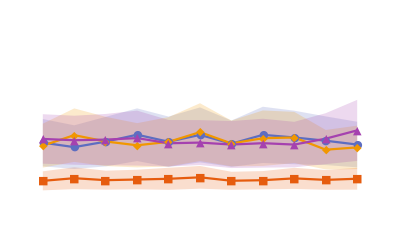

```mathematica
p1=ListPlot[Evaluate@(upper~Join~lower),Joined->True,PlotStyle->None,Filling->Table[{i->{{i+d},Directive[colors[[i]],Opacity[0.2]]}},{i,d}]];
p2=ListLinePlot[Evaluate@ys,PlotMarkers->markers,PlotStyle->colors,PlotTheme->"Scientific",GridLines->None];
p5br=Show[p1,p2,Axes->False,PlotRange->{{-10,510},{0,0.05}}]
```

```mathematica
Export["subplots/fig5b-right.png",p5br]
```

subplots/fig5b-right.png